```mathematica
rPlotsPath = "/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap4/ToEdit/";
<<Liouvillian.mx
```

## Vectorization☑

```mathematica
(*Easy to call *)
Clear[eye,tp,kp];
eye = IdentityMatrix;
tp = Transpose;
kp = KroneckerProduct;
```

```mathematica
Clear[a,coherentState];
a[Nmax_]:=Transpose[Table[If[i==j+1,Sqrt[i-1],0],{i,1,Nmax},{j,1,Nmax}]];
coherentState[α_,Ν_]:=Table[Exp[-Abs[α]^2/2]*α^n/Sqrt[n!],{n,0,Ν}]/Sqrt[Sum[Exp[-Abs[α]^2]*Abs[α]^(2n)/(n!),{n,0,Ν}]];
```

```mathematica
Clear[jump,unitary2vec,lindblad2vec];
jump [c_]:=kp[c,tp[c†]] ;
unitary2vec[H_]:=With[{ℐ = eye[Length@H]},-ⅈ (kp[H,ℐ]- kp[ℐ,tp[H]])];
lindblad2vec[L_]:=With[{ℐ = eye[Length@L]}, kp[L, tp[L†]]-1/2 kp[(L†.L),ℐ]-1/2 kp[ℐ,tp[L†.L]]];
```

Below is my way of doing the vectorization which used column stacking, it turned out to give different results from the ones Stephen has got

```mathematica
Clear[jump,unitary2vec,lindblad2vec];
jump [c_]:=kp[c*,c] ;
unitary2vec[H_]:=With[{ℐ = eye[Length@H]},-ⅈ (kp[ℐ,H]- kp[Hᵀ,ℐ])];
lindblad2vec[L_]:=With[{ℐ = eye[Length@L]}, kp[L*,L]-1/2 kp[tp[(L†.L)],ℐ]-1/2 kron[ℐ,L†.L]];
```

```mathematica
alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};
```

## Hilbert Space ☑

```mathematica
dim4LS = 4;
dimSource = 4;
dim = dim4LS dimSource^2;
(*Ordering the 4LS basis as:*)
{spinDw,spinUp,trionDw,trionUp} = {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Dipole operators*)
ΣL = Outer[Times, spinDw,trionDw]
ΣR = Outer[Times, spinUp,trionUp]
```

{{0,0,1,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}

```mathematica
(*Dipole Operators in the large Hilbert Space*)
σL = kp[ΣL, eye[dimSource], eye[dimSource]];
σR = kp[ΣL, eye[dimSource], eye[dimSource]];
```

```mathematica
(*Virtual cavity operators*)
𝕒R = kp[eye[dim4LS],a[dimSource],eye[dimSource]]//N;
𝕒L = kp[eye[dim4LS],eye[dimSource],a[dimSource]]//N;
```

## SLH for the SPI☑

```mathematica
hs = ωs (𝕒R†.𝕒R + 𝕒L†.𝕒L);
hint = -ⅈ(√(ηs κs γ))/2(σR†.𝕒R-𝕒R†.σR + σL†.𝕒L-𝕒L†.σL );
htot = hs + hint;
```

```mathematica
PrettyTiming[𝒰 = unitary2vec[htot];]
```

0h : 0m : 9s

```mathematica
PrettyTiming[𝒟γ = lindblad2vec[√γ σR + √(ηs κs)𝕒R]+lindblad2vec[√γ σL + √(ηs κs)𝕒L]+lindblad2vec[ √(1-ηs)𝕒R]+lindblad2vec[ √(1-ηs)𝕒L];]
```

0h : 0m : 59s

```mathematica
PrettyTiming[𝒟star = lindblad2vec[√γstar(σR†.σR+σL†.σL)]+lindblad2vec[√κstar(𝕒R†.𝕒R+𝕒L†.𝕒L)];]
```

0h : 0m : 26s

```mathematica
boutR = √ηt(√γ σR+√(ηs κs)𝕒R);
boutL = √ηt(√γ σL+√(ηs κs)𝕒L);
```

```mathematica
PrettyTiming[ℒ = 𝒰 + 𝒟γ + 𝒟star ;]
```

0h : 0m : 5s

```mathematica
PrettyTiming[DumpSave["Liouvillian.mx",ℒ]];
```

0h : 0m : 2s

## Fock-space exploration to dimension reduction☑ - I want to discuss

Pick up some parameter set to explore the Fock-Liouville space

```mathematica
par={ωs->0.2,ηs->0.1,κs->0.1,γ->1.,γstar->0.1,κstar->0.2,ηt->0.1};
```

```mathematica
Total[Flatten@(ℒ/.par)]
```

-7063.41+0. ⅈ

This shows that I didn’t forget to put any of the variables :)

Initial state: Choose an initial state to reduce the necessary subspace: gs spin superposition + H-polarized input coherent state (vacuum + 3 photons - Fockdim = 4)

```mathematica
istate=Flatten[kp[{1,1,0,0},Table[1,{i,1,4}],Table[1,{i,1,4}]]];
```

Vectorize it:

```mathematica
istate=Flatten[kp[istate,istate]];
```

Sign of initial state assigns 1 to positive values, 0 when the value is 0 and -1 when the value is negative.
 Range[dim^2] makes a big list going from 1 to 4096. 
 The output is a list with a bunch of zeros and the indexes of the initial nodes where the values are not zero, i.e., we known in this big guy which matrix elements are not zero and their index.

```mathematica
aux1 = Sign[istate]*Range[dim^2];
```

List with the initial nodes.

```mathematica
initialnodes=DeleteCases[aux1,0];
```

```mathematica
%
```

{1,5,9,13,17,21,25,29,257,261,265,269,273,277,281,285,513,517,521,525,529,533,537,541,769,773,777,781,785,789,793,797,1025,1029,1033,1037,1041,1045,1049,1053,1281,1285,1289,1293,1297,1301,1305,1309,1537,1541,1545,1549,1553,1557,1561,1565,1793,1797,1801,1805,1809,1813,1817,1821}

```mathematica
Head@%
```

List

This step is a bit not clear. We take the Liouvillian sum with the identity with a symbol x, then where the we have an numerical value the NumericQ gives True, and this is assigned the value zero, but False and 1 otherwise.

```mathematica
aux2= NumericQ/@Flatten[ℒ+x*eye[Length[ℒ]]]/.{True->0,False->1}
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16777136,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
 |  |  |  |

```mathematica
Head@%
Dimensions@%%
```

List

{16777216}

The adjacency matrix is computed from this guy, a partition of values 0 and 1 with the dimension of the total Fock Liouville space.

```mathematica
adjacencymatrix=Partition[aux2,dim^2];
```

```mathematica
Head@%
Dimensions@%%
```

List

{4096,4096}

This I also don’t quit understand, but in the end it is what is ploted.

```mathematica
aux3=Transpose[Sign[adjacencymatrix+Transpose[adjacencymatrix]]]
```

{1}
 |  |  |  |

```mathematica
Head@%
Dimensions@%%
```

List

{4096,4096}

```mathematica
AdjacencyGraph[aux3,
VertexStyle->Table[i->If[MemberQ[initialnodes,Range[dim^2][[i]]],Red,Black],{i,dim^2}],
PlotLabel->"Full Fock-Liouville space and intereactions for the ME",
Frame->True,
FrameLabel->{"Red dot is the initial state"}]
```

Apply the propagator once for the parameter set to check which Fock - Liouville states become populated.

```mathematica
PrettyTiming[expState=Sign[Abs[MatrixExp[ℒ/.par].istate]];]
```

0h : 0m : 27s

Finding the indexes of the populated states:

```mathematica
aux4=expState*Range[dim^2];
```

The places that were explored are indexed in the following list:

```mathematica
nodeset=DeleteCases[aux4,0];
```

```mathematica
nodeset
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024,2025,2026,2027,2028,2029,2030,2031,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2113,2114,2115,2116,2117,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2130,2131,2132,2133,2134,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2157,2158,2159,2177,2178,2179,2180,2181,2182,2183,2184,2185,2186,2187,2188,2189,2190,2191,2192,2193,2194,2195,2196,2197,2198,2199,2200,2201,2202,2203,2204,2205,2206,2207,2208,2209,2210,2211,2212,2213,2214,2215,2216,2217,2218,2219,2220,2221,2222,2223,2241,2242,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2266,2267,2268,2269,2270,2271,2272,2273,2274,2275,2276,2277,2278,2279,2280,2281,2282,2283,2284,2285,2286,2287,2305,2306,2307,2308,2309,2310,2311,2312,2313,2314,2315,2316,2317,2318,2319,2320,2321,2322,2323,2324,2325,2326,2327,2328,2329,2330,2331,2332,2333,2334,2335,2336,2337,2338,2339,2340,2341,2342,2343,2344,2345,2346,2347,2348,2349,2350,2351,2369,2370,2371,2372,2373,2374,2375,2376,2377,2378,2379,2380,2381,2382,2383,2384,2385,2386,2387,2388,2389,2390,2391,2392,2393,2394,2395,2396,2397,2398,2399,2400,2401,2402,2403,2404,2405,2406,2407,2408,2409,2410,2411,2412,2413,2414,2415,2433,2434,2435,2436,2437,2438,2439,2440,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2469,2470,2471,2472,2473,2474,2475,2476,2477,2478,2479,2497,2498,2499,2500,2501,2502,2503,2504,2505,2506,2507,2508,2509,2510,2511,2512,2513,2514,2515,2516,2517,2518,2519,2520,2521,2522,2523,2524,2525,2526,2527,2528,2529,2530,2531,2532,2533,2534,2535,2536,2537,2538,2539,2540,2541,2542,2543,2561,2562,2563,2564,2565,2566,2567,2568,2569,2570,2571,2572,2573,2574,2575,2576,2577,2578,2579,2580,2581,2582,2583,2584,2585,2586,2587,2588,2589,2590,2591,2592,2593,2594,2595,2596,2597,2598,2599,2600,2601,2602,2603,2604,2605,2606,2607,2625,2626,2627,2628,2629,2630,2631,2632,2633,2634,2635,2636,2637,2638,2639,2640,2641,2642,2643,2644,2645,2646,2647,2648,2649,2650,2651,2652,2653,2654,2655,2656,2657,2658,2659,2660,2661,2662,2663,2664,2665,2666,2667,2668,2669,2670,2671,2689,2690,2691,2692,2693,2694,2695,2696,2697,2698,2699,2700,2701,2702,2703,2704,2705,2706,2707,2708,2709,2710,2711,2712,2713,2714,2715,2716,2717,2718,2719,2720,2721,2722,2723,2724,2725,2726,2727,2728,2729,2730,2731,2732,2733,2734,2735,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2767,2768,2769,2770,2771,2772,2773,2774,2775,2776,2777,2778,2779,2780,2781,2782,2783,2784,2785,2786,2787,2788,2789,2790,2791,2792,2793,2794,2795,2796,2797,2798,2799,2817,2818,2819,2820,2821,2822,2823,2824,2825,2826,2827,2828,2829,2830,2831,2832,2833,2834,2835,2836,2837,2838,2839,2840,2841,2842,2843,2844,2845,2846,2847,2848,2849,2850,2851,2852,2853,2854,2855,2856,2857,2858,2859,2860,2861,2862,2863,2881,2882,2883,2884,2885,2886,2887,2888,2889,2890,2891,2892,2893,2894,2895,2896,2897,2898,2899,2900,2901,2902,2903,2904,2905,2906,2907,2908,2909,2910,2911,2912,2913,2914,2915,2916,2917,2918,2919,2920,2921,2922,2923,2924,2925,2926,2927,2945,2946,2947,2948,2949,2950,2951,2952,2953,2954,2955,2956,2957,2958,2959,2960,2961,2962,2963,2964,2965,2966,2967,2968,2969,2970,2971,2972,2973,2974,2975,2976,2977,2978,2979,2980,2981,2982,2983,2984,2985,2986,2987,2988,2989,2990,2991}

```mathematica
nodeset//Dimensions
```

{2209}

So, instead of working in the big big 4096 dimensional space, we can look just into this small subspace of 2209.
Building the adj matrix

```mathematica
aux5=tp[Sign[adjacencymatrix+tp[adjacencymatrix]]]
```

{1}
 |  |  |  |

Take the subset of places that where explored:

```mathematica
aux6 = aux5[[nodeset,nodeset]]
```

{1}
 |  |  |  |

```mathematica
Head@%
Dimensions@%%
```

List

{2209,2209}

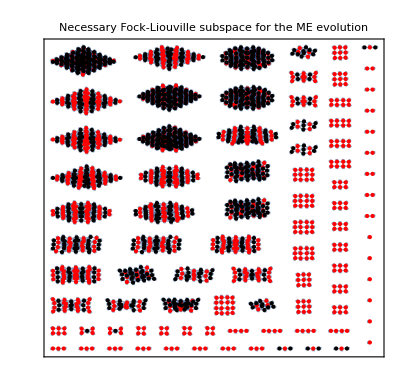

/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap4/ToEdit/qBhatNecessaryFockLiouvilleSpace.pdf

```mathematica
AdjacencyGraph[aux6,
VertexStyle->Table[i->If[MemberQ[initialnodes,nodeset[[i]]],Red,Black],{i,Length[nodeset]}],PlotLabel->"Necessary Fock-Liouville subspace for the ME evolution",
Frame->True,
FrameLabel->{"Red dots are the initial state"}]
Export[PlotsPath<>"qBhatNecessaryFockLiouvilleSpace.pdf",%]
```

## Generating data and plots☑

Once we know which nodes are populated we can reduce the dynamics of the system by addressing solely the nodes that are populated. This is accomplished by working on the subset as follows:

```mathematica
ℒSS=ℒ[[nodeset,nodeset]];
istateSS=istate[[nodeset]];
(*To tae the trace in the Foc-Liouville space*)
traceSS=Flatten[eye[dim]][[nodeset]];
```

```mathematica
Head@ℒSS
Dimensions@ℒSS
Head@istateSS
Dimensions@istateSS
Head@traceSS
Dimensions@traceSS
```

List

{2209,2209}

List

{2209}

List

{2209}

Defining the coherence operator to compute the qBhat.

```mathematica
σupdw = Outer[Times,spinDw,spinUp];
σupdw=kp[σupdw,eye[dimSource],eye[dimSource]];
σupdw=kp[σupdw,eye[dim]][[nodeset,nodeset]];
traceSS=Flatten[eye[dim]][[nodeset]];
```

Making the simulation up to the steady state. t=10^8 very long

```mathematica
qBhatcs=ParallelTable[
par={ωs->0.,ηs->1.,γ->1.,κs->10^k,κstar->0.,γstar->0.};
istate=Flatten[kp[(spinUp+spinDw)/(√2),coherentState[10^l/(√2),3],coherentState[10^l/(√2),3]]];
istate=Flatten[kp[istate,istate]][[nodeset]];

qBhatcs=2Abs[traceSS.σupdw.MatrixPower[MatrixExp[ℒSS/.par],10^8].istate];

{(10^l),10^k,qBhatcs},

{l,-1.,0,0.05},{k,-2.,1.,0.05}];
```

$Aborted

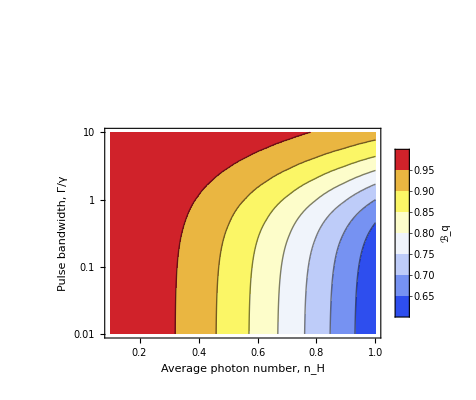

/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap4/ToEdit/qBhatcs.pdf

```mathematica
qBhatcsPlot=ListContourPlot[Flatten[qBhatcs,1],
ColorFunction->ColorData["TemperatureMap"],
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n_H",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}](*BarLegend[{"TemperatureMap",{0,1}},LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}]*),
Epilog->Inset[alphabetlabel[[1]],{0.2,5}],
 PlotLegends->Automatic]
Export[PlotsPath<>"qBhatcs.pdf",%];
Export[PlotsPath<>"qBhatcs.svg",%];
```

```mathematica
ℬqqs = Abs[1-(2 n γ)/(γ+Γ)];(*Analytical formula*)
quantumqBhat=ContourPlot[
ℬqqs/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n_H",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[2]],{0.2,5}]];

zerolineOfquantumqBhat=ContourPlot[((1-(2 n γ)/(γ+Γ))/.γ->1/.n->nn/.Γ->ΓΓ)==0,{nn,0.,1.},{ΓΓ,10^-2,10},
ContourStyle->{Dashed,AbsoluteThickness[2],White},
PlotPoints->300,
ScalingFunctions->{None,"Log"}];

qBhatqsPlot=Show[quantumqBhat,zerolineOfquantumqBhat]
Export[PlotsPath<>"qBhatqs.pdf",%];
Export[PlotsPath<>"qBhatqs.svg",%];
```

-Graphics-

```mathematica
bothqBhats = Grid[{qBhatcsPlot,qBhatqsPlot}]
Export[PlotsPath<>"qBhat.pdf",%];
```

```mathematica
qBhatqs=ParallelTable[
par={ωs->0.,ηs->1.,γ->1.,κs->10^k,κstar->0.,γstar->0.};
superposition = √(1-n){1,0,0,0}+√n{0,1,0,0};(*Issoaqui ta errado.*)
istate=Flatten[kp[(spinUp+spinDw)/(√2),superposition,{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];

qBhatqs=2Abs[traceSS.σupdw.MatrixPower[MatrixExp[ℒSS/.par],10^8].istate];

{n,10^k,qBhatqs},

{n,0,1,0.1},{k,-5.,1.,0.1}];
```

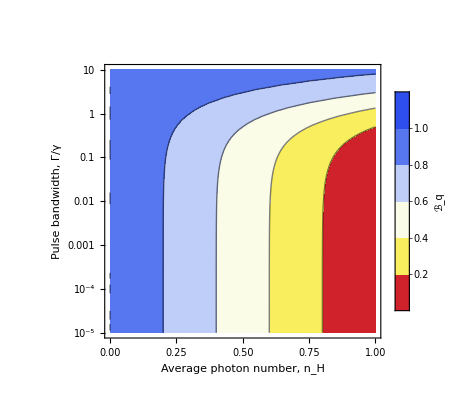

```mathematica
ListContourPlot[Flatten[qBhatqs,1],
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n_H",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[1]],{0.2,5}],
 PlotLegends->Automatic]
```

```mathematica
ℬqqs = Abs[1-(2 n γ)/(γ+Γ)];
quantumqBhat=ContourPlot[
ℬqqs/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n_H",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[2]],{0.2,5}]];

zerolineOfquantumqBhat=ContourPlot[((1-(2 n γ)/(γ+Γ))/.γ->1/.n->nn/.Γ->ΓΓ)==0,{nn,0.,1.},{ΓΓ,10^-2,10},
ContourStyle->{Dashed,AbsoluteThickness[2],White},
PlotPoints->300,
ScalingFunctions->{None,"Log"}];

qBhatqsPlot=Show[quantumqBhat,zerolineOfquantumqBhat]
Export[PlotsPath<>"qBhatqs.pdf",%];
```

-Graphics-

```mathematica
ℬqqs = Abs[1-(2 n γ)/(γ+Γ)];
quantumqBhat=ContourPlot[
ℬqqs/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
minmax={0,1.},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
ColorFunctionScaling->False,
BarLegend[{"TemperatureMap",minmax},LegendLayout->"Row",LabelStyle->Directive[Black,10,Bold]],

PlotPoints->300,

ScalingFunctions->{None,"Log"},

FrameTicksStyle->Directive["Times",FontSize->20,Black],

FrameLabel->{Style["Average photon number, n_H",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},

PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}]];

zerolineOfquantumqBhat=ContourPlot[((1-(2 n γ)/(γ+Γ))/.γ->1/.n->nn/.Γ->ΓΓ)==0,{nn,0.,1.},{ΓΓ,10^-2,10},
ContourStyle->{Dashed,AbsoluteThickness[2],White},
PlotPoints->300,
ScalingFunctions->{None,"Log"}];

qBhatqsPlot=Show[quantumqBhat,zerolineOfquantumqBhat]
Export[PlotsPath<>"qBhatqs.pdf",%];
```